```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.2.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
FileExistsQ["../../UFOandFAModels/UV_BSM_ToyModel_ren-FA/UV_BSM_ToyModel_ren-FA.mod"]
SetOptions[InsertFields, Model ->"../../UFOandFAModels/UV_BSM_ToyModel_ren-FA/UV_BSM_ToyModel_ren-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

True

## g- t- t (1-loop) VLF

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →3, with {} →{-F[9],F[9],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3}).
However the choice below produces nicer diagrams.

generic model {Lorentz} initialized

classes model {../../UFOandFAModels/UV_BSM_ToyModel_ren-FA/UV_BSM_ToyModel_ren-FA} initialized

in total: 2 Particles insertions

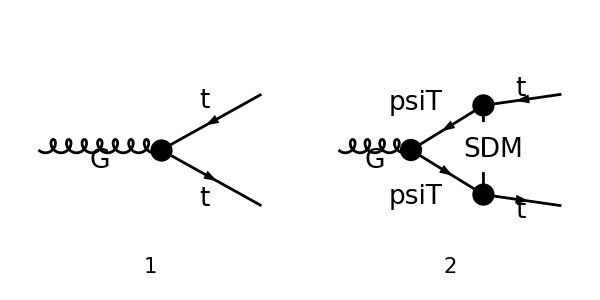

```mathematica
tops0 = CreateTopologies[0,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  {V[4]}->  {-F[9],F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampVA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3},OutgoingMomenta->{-p1,-p2},LoopMomenta->{q},List->False,SUNIndexNames->{cc3,aa,bb},SUNFIndexNames->{a,c1,c2},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs}
ampVB =FullSimplify[SUNSimplify[DiracSimplify[FCReplaceMomenta[ampVA,{p3->-p1-p2}]]]];
```

in total: 2 Particles amplitudes

(gs T_c2c1^cc3 (-p1-p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(mChi+γ·(p1+q)).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((p1+q)^2-mChi^2).((p1+p2+q)^2-mST^2))+ⅈ γ^μ.(γ̄)^7 (2 π^2 deltaCTL gs yDM^2+gs) T_c2c1^cc3+ⅈ γ^μ.(γ̄)^6 (2 π^2 deltaCTR gs yDM^2+gs) T_c2c1^cc3

```mathematica
ampVC =FCCanonicalizeDummyIndices[( TID[ampVB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify),LorentzIndexNames-> {μ,ν}]
```

ⅈ gs T_c2c1^cc3 (π^2 yDM^2 γ^μ.(γ̄)^6 B_0(p2^2,mPsiT^2,mSDM^2)+π^2 yDM^2 ((γ·p1).γ^μ.(γ·p1).(γ̄)^6-2 p1^μ (γ·p1).(γ̄)^6+(γ·p2).γ^μ.(γ·p1).(γ̄)^6) C_0(p1^2,p2^2,p1^2+2 (p1·p2)+p2^2,mPsiT^2,mSDM^2,mPsiT^2)-2 π^2 yDM^2 γ^μ.(γ̄)^6 C_00(p1^2,p2^2,2 (p1·p2)+p1^2+p2^2,mPsiT^2,mSDM^2,mPsiT^2)+π^2 yDM^2 ((γ·p1).γ^μ.(γ·p1).(γ̄)^6-4 p1^μ (γ·p1).(γ̄)^6+(γ·p2).γ^μ.(γ·p1).(γ̄)^6) C_1(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)-π^2 yDM^2 ((γ·p1).γ^μ.(γ·p2).(γ̄)^6-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6)+(γ·p2).γ^μ.(γ·p2).(γ̄)^6) C_1(p2^2,2 (p1·p2)+p1^2+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2)-2 π^2 yDM^2 p1^μ (γ·p1).(γ̄)^6 C_11(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)-2 π^2 yDM^2 p2^μ (γ·p2).(γ̄)^6 C_11(p2^2,2 (p1·p2)+p1^2+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2)+2 π^2 yDM^2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)+γ^μ.((γ̄)^6+(γ̄)^7)+2 π^2 deltaCTL yDM^2 γ^μ.(γ̄)^7+2 π^2 deltaCTR yDM^2 γ^μ.(γ̄)^6)

```mathematica
(* Remove SM contribution *)
ampSM=gs SeriesCoefficient[ampVC,{gs,0,1},{yDM,0,0}];
ampVC=Simplify[DiracSimplify[ampVC-ampSM]]
```

ⅈ gs π^2 yDM^2 (2 deltaCTL γ^μ.(γ̄)^7+C_0(p1^2,p2^2,p1^2+2 (p1·p2)+p2^2,mPsiT^2,mSDM^2,mPsiT^2) (γ·p2).γ^μ.(γ·p1).(γ̄)^6+(γ·p2).γ^μ.(γ·p1).(γ̄)^6 C_1(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)-2 (γ·p1).(γ̄)^6 p1^μ C_1(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)-(γ·p1).γ^μ.(γ·p2).(γ̄)^6 C_1(p2^2,p1^2+2 (p1·p2)+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2)+2 (γ·p2).(γ̄)^6 p1^μ C_1(p2^2,p1^2+2 (p1·p2)+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2)+2 (γ·p1).(γ̄)^6 p2^μ C_1(p2^2,p1^2+2 (p1·p2)+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2)-2 (γ·p2).(γ̄)^6 p2^μ C_1(p2^2,p1^2+2 (p1·p2)+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2)+γ^μ.(γ̄)^6 (2 deltaCTR+B_0(p2^2,mPsiT^2,mSDM^2)-C_0(p1^2,p2^2,p1^2+2 (p1·p2)+p2^2,mPsiT^2,mSDM^2,mPsiT^2) p1^2-p1^2 C_1(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)+p2^2 C_1(p2^2,p1^2+2 (p1·p2)+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2)-2 C_00(p1^2,p2^2,p1^2+2 (p1·p2)+p2^2,mPsiT^2,mSDM^2,mPsiT^2))-2 (γ·p1).(γ̄)^6 p1^μ C_11(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)-2 (γ·p2).(γ̄)^6 p2^μ C_11(p2^2,p1^2+2 (p1·p2)+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2)+2 (γ·p2).(γ̄)^6 p1^μ C_12(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)+2 (γ·p1).(γ̄)^6 p2^μ C_12(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)) T_c2c1^cc3

### Off - Shell Case

```mathematica
FCClearScalarProducts[];
```

```mathematica
SPD[p1,p2]=1/2(s-SPD[p1,p1]-SPD[p2,p2]);
```

```mathematica
ampVD=FullSimplify[DiracSimplify[FCReplaceMomenta[ampVC,{p3->-p1-p2}]]];
```

```mathematica
ampVEsimp2=FullSimplify[ExpandScalarProduct[DiracSimplify[ampVD/.{DiracGamma[7]->1-DiracGamma[6]}]]]
```

ⅈ π^2 gs yDM^2 T_c2c1^cc3 (γ^μ.(γ̄)^6 (-p1^2 (C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)+C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2))+B_0(p2^2,mPsiT^2,mSDM^2)-2 (C_00(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)+deltaCTL-deltaCTR)+p2^2 C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2))+(γ·p2).γ^μ.(γ·p1).(γ̄)^6 C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)-2 ((γ·p1).(γ̄)^6 (p1^μ (C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)+C_11(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2))-p2^μ C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2))+(γ·p2).(γ̄)^6 ((p2^μ-p1^μ) C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)+p2^μ C_11(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)))+(γ·p2).γ^μ.(γ·p1).(γ̄)^6 C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)-(γ·p1).γ^μ.(γ·p2).(γ̄)^6 C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)+2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,s,p2^2,mSDM^2,mPsiT^2,mPsiT^2)+2 deltaCTL γ^μ)

## g-t-t (1-loop) Scalar

```mathematica
FileExistsQ["../../UFOandFAModels/SMS-stop-FA/SMS-stop-FA.mod"]
SetOptions[InsertFields, Model ->"../../UFOandFAModels/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

True

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

classes model {../../UFOandFAModels/SMS-stop-FA/SMS-stop-FA} initialized

in total: 2 Particles insertions

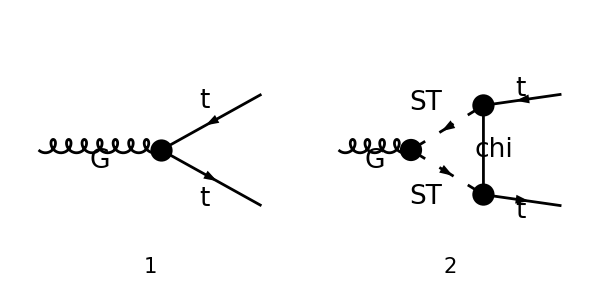

```mathematica
tops0 = CreateTopologies[0,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  {V[4]}->  {-F[9],F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampSA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3},OutgoingMomenta->{-p1,-p2},LoopMomenta->{q},List->False,SUNIndexNames->{cc3,aa,bb},SUNFIndexNames->{a,c1,c2},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampSB =FullSimplify[SUNSimplify[DiracSimplify[FCReplaceMomenta[ampSA,{p3->-p1-p2}]]]]
```

in total: 2 Particles amplitudes

gs T_c2c1^cc3 ((yDM^2 (p1^μ+p2^μ+2 q^μ) ((γ·p1).(γ̄)^6+(γ·q).(γ̄)^6))/((q^2-mST^2).((p1+q)^2-mChi^2).((p1+p2+q)^2-mST^2))+ⅈ (2 π^2 deltaCTL yDM^2+1) γ^μ.(γ̄)^7+ⅈ (2 π^2 deltaCTR yDM^2+1) γ^μ.(γ̄)^6)

```mathematica
ampSC =FCCanonicalizeDummyIndices[( TID[ampSB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify),LorentzIndexNames-> {μ,ν}]
```

ⅈ gs T_c2c1^cc3 (2 π^2 yDM^2 γ^μ.(γ̄)^6 C_00(s,p1^2,p2^2,mST^2,mST^2,mChi^2)+π^2 yDM^2 (p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(s,p1^2,p2^2,mST^2,mST^2,mChi^2)-π^2 yDM^2 (p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_1(s,p2^2,p1^2,mST^2,mST^2,mChi^2)+2 π^2 yDM^2 p1^μ (γ·p1).(γ̄)^6 C_11(s,p1^2,p2^2,mST^2,mST^2,mChi^2)+2 π^2 yDM^2 p2^μ (γ·p2).(γ̄)^6 C_11(s,p2^2,p1^2,mST^2,mST^2,mChi^2)-2 π^2 yDM^2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,s,p2^2,mChi^2,mST^2,mST^2)+γ^μ.((γ̄)^6+(γ̄)^7)+2 π^2 deltaCTL yDM^2 γ^μ.(γ̄)^7+2 π^2 deltaCTR yDM^2 γ^μ.(γ̄)^6)

```mathematica
ampSM=gs SeriesCoefficient[ampSC,{gs,0,1},{yDM,0,0}];
ampSC=Simplify[DiracSimplify[ampSC-ampSM]]
```

ⅈ π^2 gs yDM^2 T_c2c1^cc3 (2 γ^μ.(γ̄)^6 (C_00(s,p1^2,p2^2,mST^2,mST^2,mChi^2)+deltaCTR)+p1^μ (γ·p1).(γ̄)^6 C_1(s,p1^2,p2^2,mST^2,mST^2,mChi^2)-p2^μ (γ·p1).(γ̄)^6 C_1(s,p1^2,p2^2,mST^2,mST^2,mChi^2)-p1^μ (γ·p2).(γ̄)^6 C_1(s,p2^2,p1^2,mST^2,mST^2,mChi^2)+p2^μ (γ·p2).(γ̄)^6 C_1(s,p2^2,p1^2,mST^2,mST^2,mChi^2)+2 p1^μ (γ·p1).(γ̄)^6 C_11(s,p1^2,p2^2,mST^2,mST^2,mChi^2)+2 p2^μ (γ·p2).(γ̄)^6 C_11(s,p2^2,p1^2,mST^2,mST^2,mChi^2)-2 p1^μ (γ·p2).(γ̄)^6 C_12(p1^2,s,p2^2,mChi^2,mST^2,mST^2)-2 p2^μ (γ·p1).(γ̄)^6 C_12(p1^2,s,p2^2,mChi^2,mST^2,mST^2)+2 deltaCTL γ^μ.(γ̄)^7)

### Off-Shell Case

```mathematica
FCClearScalarProducts[];
```

```mathematica
SPD[p1,p2]=1/2(s-SPD[p1,p1]-SPD[p2,p2]);
```

```mathematica
ampSD=FullSimplify[DiracSimplify[FCReplaceMomenta[ampSC,{p3->-p1-p2}]]];
```

```mathematica
ampSEsimp2=FullSimplify[ExpandScalarProduct[DiracSimplify[ampSD/.{DiracGamma[7]->1-DiracGamma[6]}]]]
```

ⅈ π^2 gs yDM^2 T_c2c1^cc3 (2 γ^μ.(γ̄)^6 (C_00(s,p1^2,p2^2,mST^2,mST^2,mChi^2)-deltaCTL+deltaCTR)+(γ·p1).(γ̄)^6 (p1^μ (C_1(s,p1^2,p2^2,mST^2,mST^2,mChi^2)+2 C_11(s,p1^2,p2^2,mST^2,mST^2,mChi^2))-p2^μ (C_1(s,p1^2,p2^2,mST^2,mST^2,mChi^2)+2 C_12(p1^2,s,p2^2,mChi^2,mST^2,mST^2)))+(γ·p2).(γ̄)^6 (p2^μ (C_1(s,p2^2,p1^2,mST^2,mST^2,mChi^2)+2 C_11(s,p2^2,p1^2,mST^2,mST^2,mChi^2))-p1^μ (C_1(s,p2^2,p1^2,mST^2,mST^2,mChi^2)+2 C_12(p1^2,s,p2^2,mChi^2,mST^2,mST^2)))+2 deltaCTL γ^μ)

## Difference VLF - Scalar

```mathematica
ampDiff = (ampVB - ampSB/.{mST->mPsiT,mChi->mSDM})/.{deltaCTL->0, deltaCTR->0} //DiracSimplify //FullSimplify
```

-(gs yDM^2 T_c2c1^cc3 ((mPsiT^2-q^2) γ^μ.(γ̄)^6+(p1^μ+p2^μ) ((γ·p1).(γ̄)^6+(γ·q).(γ̄)^6)+(γ·p1).γ^μ.(γ·q).(γ̄)^6+2 q^μ ((γ·p1).(γ̄)^6+2 (γ·q).(γ̄)^6)+(γ·p2).γ^μ.(γ·q).(γ̄)^6))/((q^2-mPsiT^2).((p1+q)^2-mSDM^2).((p1+p2+q)^2-mPsiT^2))

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,PaVe}];
Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]]]},{i,1,Length[lInts]}]
```

(B_0(p2^2,mPsiT^2,mSDM^2) | 1/ε_UV
C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2) | 0
C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2) | 0
C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2) | 0
C_00(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2) | 1/(4 ε_UV)
C_11(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2) | 0
C_11(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2) | 0
C_12(p1^2,s,p2^2,mSDM^2,mPsiT^2,mPsiT^2) | 0)

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp2,PaXImplicitPrefactor->1/(2 Pi)^(4)]];
(* Divergences from counter-terms *)
Coefficient[ampEsimp2,deltaCTR];
ctUV=FullSimplify[SUNSimplify[Coefficient[ampEsimp2,deltaCTR] ] (-1/(64 π^4 EpsilonUV)) ] ;
FullSimplify[FeynAmpDenominatorExplicit[DiracSimplify[loopUV+ctUV,DiracSubstitute67->False]]]
```

0

## Coefficients for Loop Amplitude

```mathematica
args1={Pair[Momentum[p1,D],Momentum[p1,D]],s,Pair[Momentum[p2,D],Momentum[p2,D]]};
args2={mSDM^2,mPsiT^2,mPsiT^2};
argsNew={p1sq,s,p2sq};
subs2={PaVe[0,0,args1,args2,a___]->C00eff@@argsNew+deltaCTL-deltaCTR,PaVe[1,1,args1,args2,a___]->C11@@argsNew,PaVe[2,2,args1,args2,a___]->C22@@argsNew,PaVe[1,2,args1,args2,a___]->C12@@argsNew,PaVe[1,args1,args2,a___]->C1@@argsNew,PaVe[2,args1,args2,a___]->C2@@argsNew};
```

```mathematica
ampEsimp3=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp2]]/.subs2;
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]];
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains4=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
allTerms=Sort[Join[spinorChains1,spinorChains2,spinorChains3,spinorChains4]]
pairs1=Cases2[ampEsimp3,Pair];
pairs2=Flatten[Table[pairs1[[i]] pairs1[[j]],{i,1,Length[pairs1]},{j,i+1,Length[pairs1]}]];
allPairs=Join[pairs1,pairs2]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
```

{(γ̄)^6,γ^μ,γ·p1,γ·p2,γ^μ.(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,(γ·p1).γ^μ.(γ·p2).(γ̄)^6,(γ·p2).γ^μ.(γ·p1).(γ̄)^6}

{p1^μ,p2^μ,p1^2,p2^2,p1^μ p2^μ,p1^2 p1^μ,p2^2 p1^μ,p1^2 p2^μ,p2^2 p2^μ,p1^2 p2^2}

{T_c2c1^cc3}

### Coefficients for each term

Define short names for each coefficient

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]],allPairs[[k]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs yDM^2),{MT,t,u},FullSimplify];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],allPairs[[k]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]},{k,1,Length[allPairs]}];
```

We have to deal with the terms without explicit momenta separately:

```mathematica
Do[c=FullSimplify[Coefficient[Coefficient[Expand[ampEsimp3/.{Pair[LorentzIndex[μ,D],Momentum[p2,D]]->0,Pair[LorentzIndex[μ,D],Momentum[p1,D]]->0}],su3prods[[i]]],allTerms[[j]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs yDM^2),{MT,t,u},FullSimplify];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],1,c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs yDM^2  Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]]su3Terms[[i,4]],{i,1,Length[su3Terms]}];
Simplify[ampTot-ampEsimp3]
```

-ⅈ π^2 gs yDM^2 γ^μ.(γ̄)^6 T_c2c1^cc3 (p1^2 C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)+p1^2 C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)-p2^2 C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2))

```mathematica
su3Terms (*VLF*)
```

(T_c2c1^cc3 | γ^μ.(γ̄)^6 | p1^2 | -C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)-C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)
T_c2c1^cc3 | γ^μ.(γ̄)^6 | p2^2 | C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)
T_c2c1^cc3 | (γ·p1).(γ̄)^6 | p1^μ | -2 (C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)+C_11(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2))
T_c2c1^cc3 | (γ·p1).(γ̄)^6 | p2^μ | 2 (C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)+C12(p1sq,s,p2sq))
T_c2c1^cc3 | (γ·p2).(γ̄)^6 | p1^μ | 2 (C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)+C12(p1sq,s,p2sq))
T_c2c1^cc3 | (γ·p2).(γ̄)^6 | p2^μ | -2 (C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)+C_11(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2))
T_c2c1^cc3 | γ^μ | 1 | 2 deltaCTL
T_c2c1^cc3 | γ^μ.(γ̄)^6 | 1 | -p1^2 (C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)+C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2))+B_0(p2^2,mPsiT^2,mSDM^2)-2 (C_00(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)+deltaCTL-deltaCTR)+p2^2 C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)
T_c2c1^cc3 | (γ·p1).γ^μ.(γ·p2).(γ̄)^6 | 1 | -C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)
T_c2c1^cc3 | (γ·p2).γ^μ.(γ·p1).(γ̄)^6 | 1 | C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)+C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2))

## Construct ALOHA terms

UFO conventions:

ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3) ] (all momenta are incoming)
c2 = Top color = "2", c1 = Anti-Top color = "1", c3 = Gluon color = "3"
spins = [2, 2, 3], 
structure = ' P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)')
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contract to the left and the first (incoming) to the right)

```mathematica
su3Matrices=Tally[su3Terms[[All,1]]][[All,1]]
tensors=Tally[su3Terms[[All,2]]][[All,1]]
momenta=Tally[su3Terms[[All,3]]][[All,1]]
```

{T_c2c1^cc3}

{γ^μ.(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,γ^μ,(γ·p1).γ^μ.(γ·p2).(γ̄)^6,(γ·p2).γ^μ.(γ·p1).(γ̄)^6}

{p1^2,p2^2,p1^μ,p2^μ,1}

```mathematica
su3Replacements={SUNTF[{SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]-> "T(3,2,1)"};
tensorReplacements={DiracGamma[Momentum[p1,D],D].DiracGamma[6]-> "P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1)",
				   DiracGamma[Momentum[p2,D],D].DiracGamma[6]-> "P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1)",
				   DiracGamma[LorentzIndex[μ,D],D]-> "Gamma(3,2,1)",
				    DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6]-> "Gamma(3,2,-1)*ProjP(-1,1)"};
momentaReplacements={ Pair[LorentzIndex[μ,D],Momentum[p1,D]]-> "P(3,1)*",
                                           Pair[LorentzIndex[μ,D],Momentum[p2,D]]-> "P(3,2)*",1-> ""};
```

```mathematica
tensorReplacements = SortBy[tensorReplacements,-StringLength[ToString[#]]&]
momentaReplacements
```

{(γ·p1).(γ̄)^6→P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1),(γ·p2).(γ̄)^6→P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1),γ^μ.(γ̄)^6→Gamma(3,2,-1)*ProjP(-1,1),γ^μ→Gamma(3,2,1)}

{p1^μ→P(3,1)*,p2^μ→P(3,2)*,1→}

```mathematica
vertexCounter=0;
Do[
Print["------------------"];
Print[su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Print[StringJoin["FFVNP",ToString[vertexCounter]]];
(* Print[tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n   + "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*( ",fullStr," )"];
 Print[fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
```

------------------

T(3,2,1)

FFVNP1

( P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1) )*( P(3,1)*(-2*(C1(p1sq,s,p2sq) + C11(p1sq,s,p2sq)))\
   + P(3,2)*(2*(C1(p1sq,s,p2sq) + C12(p1sq,s,p2sq))) )

FFVNP2

( P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1) )*( P(3,1)*(2*(C1(p1sq,s,p2sq) + C12(p1sq,s,p2sq)))\
   + P(3,2)*(-2*(C1(p1sq,s,p2sq) + C11(p1sq,s,p2sq))) )

FFVNP3

( Gamma(3,2,1) )*( (2*deltaCTL) )

FFVNP4

( Gamma(3,2,-1)*ProjP(-1,1) )*( (B0(MT**2,mPsiT**2,mSDM**2) - MT**2*C0(MT**2,MT**2,s,mPsiT**2,mSDM**2,mPsiT**2) - 2*(deltaCTL - deltaCTR + PaVe(0,0,List(MT**2,MT**2,s),List(mPsiT**2,mSDM**2,mPsiT**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)))) )

FFVNP5

StringJoin::string: String expected at position 2 in ( <>((γ·p1).γ^μ.P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1))<> )*( (-C1(p1sq,s,p2sq)) ).

( <>((γ·p1).γ^μ.P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1))<> )*( (-C1(p1sq,s,p2sq)) )

FFVNP6

StringJoin::string: String expected at position 2 in ( <>((γ·p2).γ^μ.P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1))<> )*( (C0(MT**2,MT**2,s,mPsiT**2,mSDM**2,mPsiT**2) + C1(p1sq,s,p2sq)) ).

( <>((γ·p2).γ^μ.P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1))<> )*( (C0(MT**2,MT**2,s,mPsiT**2,mSDM**2,mPsiT**2) + C1(p1sq,s,p2sq)) )

#### Write to File

```mathematica
fileName="../../UFOandFAModels/Top-FormFactorsOneLoop-UFO/lffvnp.txt";
outF = OpenWrite[fileName,PageWidth->Infinity];
vertexCounter=0;
Do[
Write[outF,"------------------"];
Write[outF,su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Write[outF,StringJoin["FFVNP",ToString[vertexCounter]]];
(* Write[outF,tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n   + "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*( ",fullStr," )"];
 Write[outF,fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
Close[outF]
```

OpenWrite::noopen: Cannot open ../../UFOandFAModels/Top-FormFactorsOneLoop-UFO/lffvnp.txt.

Write::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of Write::strml will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[p1^2].

StringJoin::string: String expected at position 1 in p1^2<>(-C0(Pair(Momentum(p1,D),Momentum(p1,D)),Pair(Momentum(p2,D),Momentum(p2,D)),s,mPsiT**2,mSDM**2,mPsiT**2) - PaVe(1,List(s,Pair(Momentum(p1,D),Momentum(p1,D)),Pair(Momentum(p2,D),Momentum(p2,D))),List(mPsiT**2,mPsiT**2,mSDM**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)))\
   + .

StringJoin::string: String expected at position 1 in StringJoin[p2^2].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close[$Failed]

## On - Shell Regime and Degenerate

```mathematica
SPD[p1,p1]=MT^2;
SPD[p2,p2]=MT^2;
```

```mathematica
SubsCT={deltaCTL-> -1/(128 Subscript[g, s] √lA π^6 xT^2 Subscript[y, DM]^2)ⅈ (√lA xT (2-2 xC+xT)+√lA (1+xC^2-xC (2+xT)) Log[xC]+((-1+xC)^3+(1+xC-2 xC^2) xT+xC xT^2) (Log[4]+Log[xC]-2 Log[1+xC-xT+√((-1+xC)^2-2 (1+xC) xT+xT^2)])),deltaCTR-> 1/(128 √lA π^4 xT^2)(√lA ((-1+xC)^2+xT^2) Log[xC]-2 (-1+xC+xT) (√lA xT+(1+xC^2+xT^2-2 xC (1+xT)) Log[(1+√lA+xC-xT)/(2 √xC)])),xC-> 1,xT-> 0,lA-> (1+xC^2+xT^2-2*xC-2*xT-2*xT*xC)};
```

```mathematica
Limit[Limit[deltaCTL/.SubsCT/.lA-> xC^2+(1-xT)^2-2*xC*(1+xT),xC->1],xT->0]
Limit[Limit[deltaCTR/.SubsCT/.lA-> xC^2+(1-xT)^2-2*xC*(1+xT),xC->1],xT->0]
```

0

0

```mathematica
ampEsimpOnShell = FullSimplify[ampEsimp2/(I Pi^2 gs yDM^2)]
```

T_c2c1^cc3 (γ^μ.(γ̄)^6 (B_0(MT^2,mPsiT^2,mSDM^2)+MT^2 (-C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2))-2 (C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+deltaCTL-deltaCTR))+(γ·p2).γ^μ.(γ·p1).(γ̄)^6 C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)-(γ·p1).γ^μ.(γ·p2).(γ̄)^6 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+(γ·p2).γ^μ.(γ·p1).(γ̄)^6 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+2 (p1^μ-p2^μ) ((γ·p2).(γ̄)^6-(γ·p1).(γ̄)^6) C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)-2 (p1^μ (γ·p1).(γ̄)^6+p2^μ (γ·p2).(γ̄)^6) C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+2 deltaCTL γ^μ)

```mathematica
loopFuncs = Cases[ampEsimpOnShell,_B0|_C0|_PaVe,Infinity]//DeleteDuplicates
```

{C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2),C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2),B_0(MT^2,mPsiT^2,mSDM^2),C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2),C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2),C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)}

```mathematica
loopFuncsEFT1=Table[FullSimplify[PaXEvaluate[loopFuncs[[i]],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{mSDM,mPsiT,0}}]/.{EulerGamma->0,ScaleMu->mPsiT/(√(4 Pi))}],{i,1,Length[loopFuncs]}]
```

{(log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)))/(32 π^4 s),(√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s)/(16 π^4 s^2),1/(16 π^4 ε),(ε log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) (√(s (s-4 mPsiT^2))+mPsiT^2 log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)))+3 ε s+s)/(64 π^4 ε s),-(√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s)/(32 π^4 s^2),(mPsiT^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+s)/(32 π^4 s^2)}

```mathematica
loopSubs = Table[loopFuncs[[i]]-> loopFuncsEFT1[[i]],{i,1,Length[loopFuncs]}];
```

```mathematica
ampEFT1 =Collect[Simplify[ ampEsimpOnShell/.loopSubs/.{deltaCTL->0,deltaCTR->0}],{Epsilon,s,mPsiT,Log[a_],deltaCTL,deltaCTR},Simplify]
```

(-(log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) T_c2c1^cc3 (MT^2 γ^μ.(γ̄)^6-(γ·p2).γ^μ.(γ·p1).(γ̄)^6))/(32 π^4)-(mPsiT^2 γ^μ.(γ̄)^6 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) T_c2c1^cc3)/(32 π^4)-(√(s (s-4 mPsiT^2)) γ^μ.(γ̄)^6 log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) T_c2c1^cc3)/(32 π^4)-(T_c2c1^cc3 (2 p1^μ (γ·p1).(γ̄)^6+2 (γ·p1).γ^μ.(γ·p2).(γ̄)^6-2 (γ·p2).γ^μ.(γ·p1).(γ̄)^6-5 p1^μ (γ·p2).(γ̄)^6-5 p2^μ (γ·p1).(γ̄)^6+2 p2^μ (γ·p2).(γ̄)^6))/(16 π^4))/s+((mPsiT^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) T_c2c1^cc3 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6))/(16 π^4)-(√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) T_c2c1^cc3 (p1^μ (γ·p1).(γ̄)^6+(γ·p1).γ^μ.(γ·p2).(γ̄)^6-(γ·p2).γ^μ.(γ·p1).(γ̄)^6-2 p1^μ (γ·p2).(γ̄)^6-2 p2^μ (γ·p1).(γ̄)^6+p2^μ (γ·p2).(γ̄)^6))/(16 π^4))/s^2+(γ^μ.(γ̄)^6 T_c2c1^cc3)/(32 π^4 ε)-(3 γ^μ.(γ̄)^6 T_c2c1^cc3)/(32 π^4)

```mathematica
ampEFT1b=FullSimplify[ampEFT1]
```

-1/(32 π^4 ε s^2)T_c2c1^cc3 (s γ^μ.(γ̄)^6 (ε (mPsiT^2+MT^2) log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+ε √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+(3 ε-1) s)+ε (-(s (log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+4)+2 √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))) (γ·p2).γ^μ.(γ·p1).(γ̄)^6+2 (γ·p2).(γ̄)^6 (p2^μ (√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s)-p1^μ (mPsiT^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+5 s))+2 (γ·p1).(γ̄)^6 (p1^μ (√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s)-p2^μ (mPsiT^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+5 s))+2 (√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s) (γ·p1).γ^μ.(γ·p2).(γ̄)^6))

```mathematica
ampEFT1c = Collect[ampEFT1b/.{Log[(√(s(s-4 mPsiT^2))+2 mPsiT^2 -s)/(2 mPsiT^2)]->L[s,mPsiT],√(s(s-4 mPsiT^2))->Δ[s,mPsiT]},{Epsilon},FullSimplify]
```

(γ^μ.(γ̄)^6 T_c2c1^cc3)/(32 π^4 ε)-1/(32 π^4 s^2)T_c2c1^cc3 (s (mPsiT^2+MT^2) γ^μ.(γ̄)^6 (L(s,mPsiT))^2+2 (γ·p2).(γ̄)^6 (p2^μ (L(s,mPsiT) Δ(s,mPsiT)+2 s)-p1^μ (mPsiT^2 (L(s,mPsiT))^2+2 L(s,mPsiT) Δ(s,mPsiT)+5 s))+2 (γ·p1).(γ̄)^6 (p1^μ (L(s,mPsiT) Δ(s,mPsiT)+2 s)-p2^μ (mPsiT^2 (L(s,mPsiT))^2+2 L(s,mPsiT) Δ(s,mPsiT)+5 s))+2 (L(s,mPsiT) Δ(s,mPsiT)+2 s) (γ·p1).γ^μ.(γ·p2).(γ̄)^6-(2 L(s,mPsiT) Δ(s,mPsiT)+s ((L(s,mPsiT))^2+4)) (γ·p2).γ^μ.(γ·p1).(γ̄)^6+s γ^μ.(γ̄)^6 L(s,mPsiT) Δ(s,mPsiT)+3 s^2 γ^μ.(γ̄)^6)

```mathematica
ampScalar = 1/(32 π^4 s^2)(mST^2 (L(s,mPsiT))^2+ Δ[s,mPsiT]L(s,mPsiT)+3 s) Subscript[T, c2c1]^cc3 (s (γ^μ).(γ̄)^6-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6));
FullSimplify[ampEFT1c - ampScalar]
```

-1/(32 π^4)(1/s^2 T_c2c1^cc3 (s (mPsiT^2+MT^2) γ^μ.(γ̄)^6 (L(s,mPsiT))^2+2 (γ·p2).(γ̄)^6 (p2^μ (L(s,mPsiT) Δ(s,mPsiT)+2 s)-p1^μ (mPsiT^2 (L(s,mPsiT))^2+2 L(s,mPsiT) Δ(s,mPsiT)+5 s))+2 (γ·p1).(γ̄)^6 (p1^μ (L(s,mPsiT) Δ(s,mPsiT)+2 s)-p2^μ (mPsiT^2 (L(s,mPsiT))^2+2 L(s,mPsiT) Δ(s,mPsiT)+5 s))+2 (L(s,mPsiT) Δ(s,mPsiT)+2 s) (γ·p1).γ^μ.(γ·p2).(γ̄)^6-(2 L(s,mPsiT) Δ(s,mPsiT)+s ((L(s,mPsiT))^2+4)) (γ·p2).γ^μ.(γ·p1).(γ̄)^6+s γ^μ.(γ̄)^6 L(s,mPsiT) Δ(s,mPsiT)+3 s^2 γ^μ.(γ̄)^6)+(T_(c1 c2)^cc3 (L(s,mPsiT) (mST^2 L(s,mPsiT)+Δ(s,mPsiT))+3 s) (s γ^μ.(γ̄)^6-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6)))/s^2-(γ^μ.(γ̄)^6 T_c2c1^cc3)/ε)

```mathematica
(*1. Define the Scalar Function S(s) that dominates the Article term*)(*This matches your Group 1 Coefficient exactly*)
Sfunc=mPsiT^2*L^2+L*Delta+3*s;

(*2. Define Your Full Coefficients (From your calculation)*)
(*C1:Coefficient of s*Gamma*)
Coeff1=mPsiT^2*L^2+L*Delta+3*s;

(*C2:Coefficient of Mixed Vectors (p1^mu p2_slash+p2^mu p1_slash)*)
(*Note:Your expression had-2*(...)*)
Coeff2=-2*(mPsiT^2*L^2+2*L*Delta+5*s);

(*C3:Coefficient of Sandwich 2->1*)
Coeff3=-(2*L*Delta+s*(L^2+4));

(*C4:Coefficient of Sandwich 1->2*)
Coeff4=2*(L*Delta+2*s);

(*C5:Coefficient of Diagonal Vectors (p1^mu p1_slash+...)*)
Coeff5=2*(L*Delta+2*s);

(*3. Define the Structures (Abstractly)*)
Struct1=s*GammaMu;
Struct2=(p1Slash*p2Mu+p2Slash*p1Mu);
Struct3=Sandwich21;
Struct4=Sandwich12;
Struct5=DiagVectors;

(*4. Construct the Full Bracket Content*)
FullContent=Coeff1*Struct1+Coeff2*Struct2+Coeff3*Struct3+Coeff4*Struct4+Coeff5*Struct5;

(*5. Construct the "Article" Part*)
(*The article assumes the Form Factor S(s) multiplies (s*Gamma-2*MixedVec)*)
ArticlePart=Sfunc*(-Struct1+2*Struct2);

(*6. Calculate the "Other Terms" (The Correction)*)
(*We simply subtract the Article Part from the Full Content*)
CorrectionTerms=Simplify[FullContent-ArticlePart];

(*7. Output the Result in the Requested Format*)
Print["\n--- DECOMPOSITION RESULT ---\n"];
Print["The expression can be written exactly as:"];
Print["\nPreFactor * ("];
Print["   ",Sfunc," * ( ",-Struct1+2*Struct2," )"];
Print["   + CorrectionTerms"];
Print[")\n"];

Print["\n--- EXPLICIT CORRECTION TERMS ---\n"];
Print[CorrectionTerms];

(*8. Verification step*)
Print["\n--- VERIFICATION ---"];
Print["Does (ArticlePart + CorrectionTerms) == FullContent?"];
Print[Simplify[ArticlePart+CorrectionTerms==FullContent]];
```

--- DECOMPOSITION RESULT ---

The expression can be written exactly as:

PreFactor * (

L^2 mPsiT^2+Delta L+3 s * ( 2 (p1Slash p2Mu+p1Mu p2Slash)-GammaMu s )

+ CorrectionTerms

)

--- EXPLICIT CORRECTION TERMS ---

2 Delta L (DiagVectors+GammaMu s-3 p1Mu p2Slash-3 p1Slash p2Mu+Sandwich12-Sandwich21)+2 s (2 DiagVectors+3 GammaMu s-8 p1Mu p2Slash-8 p1Slash p2Mu+2 Sandwich12-2 Sandwich21)-(L^2 (mPsiT^2 (-2 GammaMu s+4 p1Mu p2Slash+4 p1Slash p2Mu)+s Sandwich21))

--- VERIFICATION ---

Does (ArticlePart + CorrectionTerms) == FullContent?

True

```mathematica
ruleOnShell={GSD[p1].u[p1]->MT*u[p1],uBar[p2].GSD[p2]->MT*uBar[p2]};
ampEFT1c=ampEFT1b//.ruleOnShell;
organizedAmp=Collect[ampEFT1c,{Ga[mu],FV[p1,mu],FV[p2,mu]},Simplify]
coeffList={"Gamma Term"->Coefficient[organizedAmp,Ga[mu]],"p1 Vector Term"->Coefficient[organizedAmp,FV[p1,mu]],"p2 Vector Term"->Coefficient[organizedAmp,FV[p2,mu]]};
TableForm[coeffList]
```

-1/(32 π^4 ε s^2)T_c2c1^cc3 (s γ^μ.(γ̄)^6 (ε (mPsiT^2+MT^2) log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+ε √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+(3 ε-1) s)+ε (-(s (log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+4)+2 √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))) (γ·p2).γ^μ.(γ·p1).(γ̄)^6+2 (γ·p2).(γ̄)^6 (p2^μ (√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s)-p1^μ (mPsiT^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+5 s))+2 (γ·p1).(γ̄)^6 (p1^μ (√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s)-p2^μ (mPsiT^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+5 s))+2 (√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s) (γ·p1).γ^μ.(γ·p2).(γ̄)^6))

Gamma Term→0
p1 Vector Term→0
p2 Vector Term→0

Generating Plot 1: Real Parts...

Generating Plot 2: Imaginary Parts...

Generating Plot 3: Absolute Magnitudes...

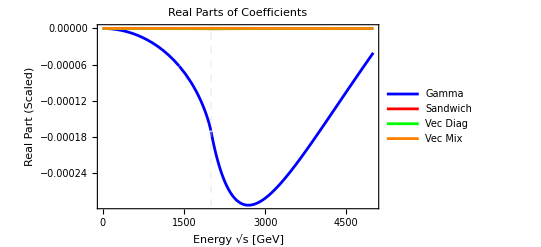
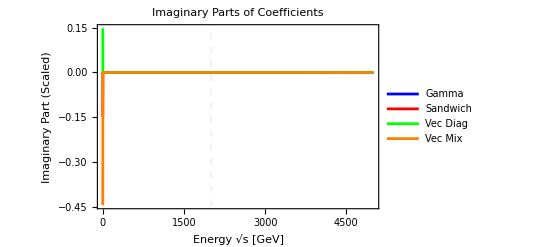
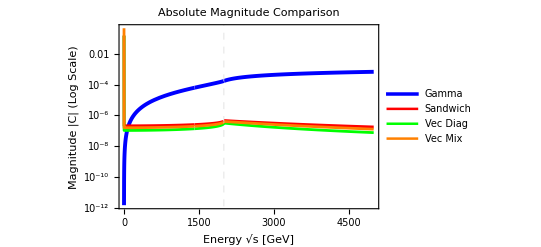

```mathematica
(*0. CLEANUP AND DEFINITIONS*)ClearAll[s,mPsiT,MT,Lfunc,Delfunc,GlobalScale,CoeffGamma,CoeffSandwich,CoeffVecDiag,CoeffVecMix];

(*Parameters*)
valMPsi=1000; (*Mass scale (mT)*)
valMT=0;      (*Top mass approx*)
MaxEnergy=5*valMPsi; (*Plot up to 5 TeV*)

(*The Global Scaling Factor from your expression*)
GlobalScale[s_]:=-1/(32*Pi^4*s^2);

(*1. DEFINE KINEMATIC FUNCTIONS*)
Lfunc[s_]:=Log[(2*valMPsi^2-s+Sqrt[s*(s-4*valMPsi^2)])/(2*valMPsi^2)];
Delfunc[s_]:=Sqrt[s*(s-4*valMPsi^2)];
valL[s_]:=Lfunc[s];
valDel[s_]:=Delfunc[s];

(*2. DEFINE THE 4 COEFFICIENTS (GROUPS)*)

(*Group 1:Gamma Term (Dimensionless)*)
CoeffGamma[s_]:=GlobalScale[s]*s*((valMPsi^2+valMT^2)*valL[s]^2+valL[s]*valDel[s]+3*s);

(*Group 2:Sandwich Term (Dimension-1)*)
(*We multiply by valMPsi to make it dimensionless and visible on the same scale*)
CoeffSandwich[s_]:=(GlobalScale[s]*-1*(s*(valL[s]^2+4)+2*valL[s]*valDel[s]))*valMPsi;

(*Group 3:Diagonal Vector Term (Dimension-1)*)
CoeffVecDiag[s_]:=(GlobalScale[s]*2*(valL[s]*valDel[s]+2*s))*valMPsi;

(*Group 4:Mixed Vector Term (Dimension-1)*)
CoeffVecMix[s_]:=(GlobalScale[s]*-2*(valMPsi^2*valL[s]^2+2*valL[s]*valDel[s]+5*s))*valMPsi;


(*3. PLOT 1:REAL PARTS (Comparison)*)
Print["Generating Plot 1: Real Parts..."];
PlotReal=Plot[{Re[CoeffGamma[s^2]],Re[CoeffSandwich[s^2]],Re[CoeffVecDiag[s^2]],Re[CoeffVecMix[s^2]]},{s,valMT,MaxEnergy},PlotRange->All,Frame->True,FrameLabel->{"Energy \!\(\*SqrtBox[\(s\)]\) [GeV]","Real Part (Scaled)"},PlotStyle->{Blue,Red,Green,Orange},PlotLegends->Placed[{"Gamma","Sandwich","Vec Diag","Vec Mix"},Above],GridLines->{{2*valMPsi},None},GridLinesStyle->Dashed,PlotLabel->"Real Parts of Coefficients"];

(*4. PLOT 2:IMAGINARY PARTS (Comparison)*)
Print["Generating Plot 2: Imaginary Parts..."];
PlotImag=Plot[{Im[CoeffGamma[s^2]],Im[CoeffSandwich[s^2]],Im[CoeffVecDiag[s^2]],Im[CoeffVecMix[s^2]]},{s,valMT,MaxEnergy},PlotRange->All,Frame->True,FrameLabel->{"Energy \!\(\*SqrtBox[\(s\)]\) [GeV]","Imaginary Part (Scaled)"},PlotStyle->{Blue,Red,Green,Orange},PlotLegends->Placed[{"Gamma","Sandwich","Vec Diag","Vec Mix"},Above],GridLines->{{2*valMPsi},None},GridLinesStyle->Dashed,PlotLabel->"Imaginary Parts of Coefficients"];

(*5. PLOT 3:ABSOLUTE MAGNITUDES (Log Scale)*)
Print["Generating Plot 3: Absolute Magnitudes..."];
PlotAbs=LogPlot[{Abs[CoeffGamma[s^2]],Abs[CoeffSandwich[s^2]],Abs[CoeffVecDiag[s^2]],Abs[CoeffVecMix[s^2]]},{s,valMT,MaxEnergy},PlotRange->All,Frame->True,FrameLabel->{"Energy \!\(\*SqrtBox[\(s\)]\) [GeV]","Magnitude |C| (Log Scale)"},PlotStyle->{{Blue,Thickness[0.007]},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Orange,Thickness[0.005]}},PlotLegends->Placed[{"Gamma","Sandwich","Vec Diag","Vec Mix"},Above],GridLines->{{2*valMPsi},None},GridLinesStyle->Dashed,PlotLabel->"Absolute Magnitude Comparison"];

(*SHOW ALL*)
{PlotReal,PlotImag,PlotAbs}
```

## Get Counter Term Expressions for LATEX:

```mathematica
deltaCTLexp=FullSimplify[(deltaCTL/.SubsCT)/.{xC->x,xT-> Subscript[x, t],lA-> λ}]
```

(2 √λ (x_t (x_t+2 x+log(x)-2)-(x-1)^2 log(x))-4 (x_t (x_t+x^2+x-2)-(x-1)^3) log((√λ-x_t+x+1)/(2 √x)))/(128 π^4 √λ x_t^2)

```mathematica
TeXForm[deltaCTLexp]
```

\frac{2 \sqrt{\lambda } \left(x_t \left(x_t+2 x+\log (x)-2\right)-(x-1)^2 \log (x)\right)-4 \left(x_t
   \left(x_t+x^2+x-2\right)-(x-1)^3\right) \log \left(\frac{\sqrt{\lambda }-x_t+x+1}{2 \sqrt{x}}\right)}{128 \pi
   ^4 \sqrt{\lambda } x_t^2}

```mathematica
deltaCTRexp=FullSimplify[deltaCTR/.SubsCT/.{xC->x,xT-> Subscript[x, t],lA-> λ}]
```

((-x_t+x-1) (2 ((x_t-1)^2+(x-2) x) log((√λ-x_t+x+1)/(2 √x))+√λ (2 x_t-(x_t+x-1) log(x))))/(128 π^4 √λ x_t^2)

```mathematica
TeXForm[deltaCTRexp]
```

\frac{\left(-x_t+x-1\right) \left(2 \left(\left(x_t-1\right){}^2+(x-2) x\right) \log \left(\frac{\sqrt{\lambda
   }-x_t+x+1}{2 \sqrt{x}}\right)+\sqrt{\lambda } \left(2 x_t-\left(x_t+x-1\right) \log (x)\right)\right)}{128 \pi
   ^4 \sqrt{\lambda } x_t^2}

```mathematica
lAexp = (1-2*xC+xC^2-2*xT-2*xC*xT+xT^2)/.{xC->x,xT-> Subscript[x, t],lA-> λ}
```

-2 x x_t+x_t^2-2 x_t+x^2-2 x+1

```mathematica
TeXForm[lAexp]
```

-2 x x_t+x_t^2-2 x_t+x^2-2 x+1